Kaushik Chakram 
                                                                                                                     Professor Julia Kamenetzky
                                                                                                                     phys 425 &01
                                                                                                                     February 27,2018

```mathematica
$Assumptions = {x,A,a,k,Subscript[A, 1],Subscript[a, 1],Subscript[a, 2],m,ℏ,t,w} ∈ Reals
```

(x|A|a|k|A_1|a_1|a_2|m|ℏ|t|w)∈Reals

Problem 1) 2.21 part a) && is used to indicate and conditions.

```mathematica
ψ[x_]:= A*(ⅇ^(-a*Abs[x]))
Assuming[(A >0 && a  >0),Integrate[Conjugate[ψ[x]]*ψ[x],{x,-∞,∞}]]
```

A^2/a

Problem  1) 2.21 part b)

```mathematica
Assuming[(k>0 && a  >0),Integrate[(√(a/(2*π)))*(ⅇ^(-a*Abs[x]))*(e^(-ⅈ*k*x)),{x,-∞,∞}]]
```

(a^(3/2) √(2/π))/((a-ⅈ k Log[e]) (a+ⅈ k Log[e]))

Problem 2) 2.22 part a)

```mathematica
Subscript[ψ, 1][x_]:= Subscript[A, 1]*(ⅇ^(-Subscript[a, 1]*x^2))
Assuming[(Subscript[A, 1] >0 && Subscript[a, 1]  >0),Integrate[Conjugate[Subscript[ψ, 1][x]]*Subscript[ψ, 1][x],{x,-∞,∞}]]
```

(√(π/2) A_1^2)/(√a_1)

Problem 2) 2.22) part b) sketch |Ψ(x,0)|^2  and |Ψ(x,t)|^2 for a very large value of t. Let a_2=ℏ=m=1 for the plots  and these are coded in as a_2= c , ℏ= d, m= f.

```mathematica
g[t_]:= √(1+((2*ⅈ*ℏ*Subscript[a, 2]*t)/m))
K1[x_,t_]:= ((2*Subscript[a, 2])/π)^(1/4)*(1/g[t])*(ⅇ^((-(Subscript[a, 2]*x^2))/(g[t])^2))
c:=1
d:=1
f:= 1
g2[t_]:= √(1+((2*ⅈ*d*c*t)/f))
K2[x_,t_]:= ((2*c)/π)^(1/4)*(1/g2[t])*(ⅇ^((-(c*x^2))/(g2[t])^2))
```

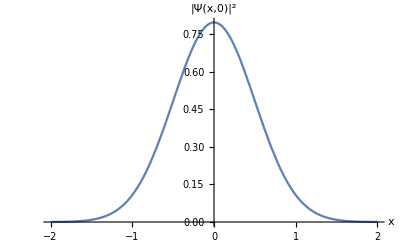

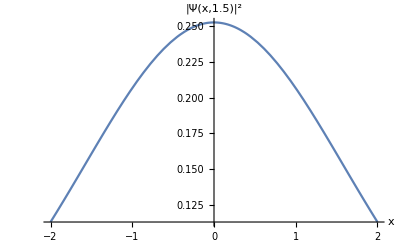

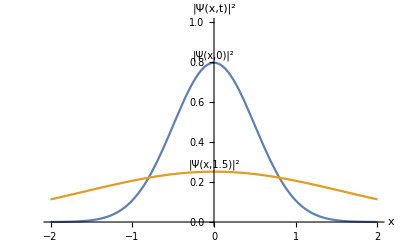

```mathematica
Plot[ (Conjugate[K2[x,0]])*(K2[x,0]),{x,-2,2},AxesLabel->{x,"|Ψ(x,0)|^2"},AxesStyle->Directive[Black, 14]]
Plot[ (K2[x,1.5])*(Conjugate[K2[x,1.5]]),{x,-2,2},AxesLabel->{x,"|Ψ(x,1.5)|^2"},AxesStyle->Directive[Black, 14]]
Plot[{(Conjugate[K2[x,0]])*(K2[x,0]),(Conjugate[K2[x,1.5]])*(K2[x,1.5])},{x,-2,2},PlotLabels-> Placed[{"|Ψ(x,0)|^2","|Ψ(x,1.5)|^2"},Above],LabelStyle->Directive[Black, 10], AxesLabel->{x,"|Ψ(x,t)|^2"},AxesStyle->Directive[Black, 12],PlotRange->{0,1}]
```

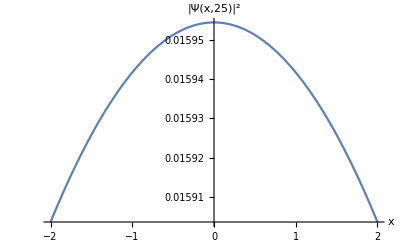

```mathematica
Plot[ (K2[x,25])*(Conjugate[K2[x,25]]),{x,-2,2},AxesLabel->{x,"|Ψ(x,25)|^2"},AxesStyle->Directive[Black, 14]]
```

```mathematica
Integrate[Conjugate[K1[x,t]]*x*K1[x,t],{x,-∞,∞}] (*it matches.*)
```

ConditionalExpression[0,a_2>0&&m≠0]

```mathematica
Integrate[Conjugate[K1[x,t]]*(ℏ/ⅈ)D[K1[x,t],{x,1}],{x,-∞,∞}]
```

ConditionalExpression[0,a_2>0&&m≠0]

```mathematica
w:=√(Subscript[a, 2]/(1+((2*ℏ*Subscript[a, 2]*t)/m)^2))
```

```mathematica
probabilitydensity[x_,t_]:=√(2/π)*(w)*(ⅇ^(-2*w^2*x^2))
Assuming[w > 0  && Subscript[a, 2]>0,Integrate[x^2*(probabilitydensity[x,t]),{x,-∞,∞}]](* multiply the first term by m^2 and factor m^2 on the numerator and the second term by 4*Subscript[a, 2] to find the common denominator. Then we can cancel m^2 adn this matches with answer found using integral sheet.*)
```

1/(4 a_2)+(t^2 ℏ^2 a_2)/m^2

```mathematica
Assuming[Subscript[a, 2]>0 && m >0,Integrate[(ℏ/ⅈ)^2 Conjugate[K1[x,t]]*D[K1[x,t],{x,2}],{x,-∞,∞}] ](* This does simplify to a*ℏ^2*)
```

ℏ^2 Conjugate[1/(√(m+2 ⅈ t ℏ a_2))] a_2 √(m-2 ⅈ t ℏ a_2)

Problem 3) 2.23) part a) There is a function command for the the delta function called DiracDelta so let’s confirm our calculations.

```mathematica
Integrate[(x^3-3*x^2+2*x-1)*DiracDelta[x + 2],{x,-3,1}]
```

-25

```mathematica
Integrate[(Cos[3*x]+2)*DiracDelta[x-π],{x,0,∞}]
```

1

```mathematica
Integrate[(ⅇ^(Abs[x]+3))*DiracDelta[x - 2],{x,-1,1}]
```

0

```mathematica
Integrate[(1/(2π))^(1/2)*e^(-ⅈ*k*x)*DiracDelta[x],{x,-∞,∞}]
```

1/(√(2 π))